# Solution of Exam #3 on Stochastic Processes and Non-Equilibrium Statistical Physics

Hernán Fernández García
hernan.fg96@gmail.com

Instituto Balseiro
Nov/09/2020

## Author Note: The latest version of this notebook is to be always available here. Any other version should automatically update to it when open.

## Defaults

```mathematica
Do[
SetOptions[funct,Frame->True,FrameTicks->{True,True},FrameTicksStyle->Directive[Thick,18],ImageMargins->5,ImageSize->Large,LabelStyle->20,PlotRange->All,Axes->False];
,{funct,{Plot,ListPlot,ListLinePlot,Histogram}}]
```

## Introduction

In this work, we study the stochastic process given by the Langevin equation

-Graphics-

under ITO calculus (α = 1), which leads to the Fokker-Planck equation for the evolution of the probability density  P(x,t)

-Graphics-

where we  have used the relations between Langevin and Fokker-Planck functions

-Graphics-

valid under ITO calculus.

From here, the distribution corresponding to the asymptotic stationary state, can be obtained be taking the zero time-derivative

-Graphics-

which results in the time-independent relation for the stationary distribution P(x).

-Graphics-

Here, by evaluating on point x = 0,  it can be shown that it must be  c = 0,  as long as

-Graphics-

which can be checked a posteriori.

Then, x factors cancel out, and it takes the easier form

both of whose members can be directly integrated

-Graphics-

Finally, the multiplicative constant A  is determined by the normalization condition of the probability density

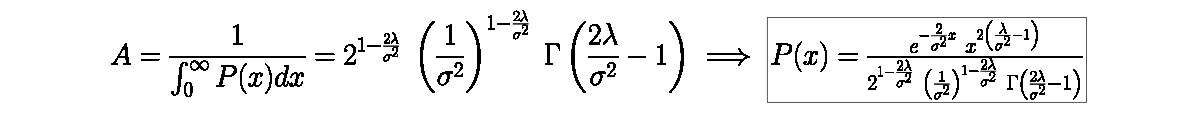

* now it can be checked that P(x) has indeed the desired behavior at x = 0

The integration limits are the boundaries of the domain of the stochastic variable x, which is taken to be

-Graphics-

since the condition g(0) = 0 makes the point x = 0 an intrinsic boundary of the F-P equation. The other intrinsic boundary would be located at +∞, in this case because |h(+∞)| → +∞

## Definitions

Let' s first define the analytical stationary PDF function, in terms of arbitrary parameters λ and σ

```mathematica
P[x_]:=(x^(2(λ/σ^2-1)) E^(-2/σ^2x))/(2^(1-(2 λ)/σ^2) (1/σ^2)^(1-(2 λ)/σ^2) Gamma[-1+(2 λ)/σ^2]);
```

then fix some numerical values for the physical parameters  (** it must always be  λ > σ^2/2, otherwise the normalization of P(x) cannot be fulfilled)

```mathematica
λ=3;
σ=2;
```

as well as simulation coefficients: measurement time (T), time-step (Δ) and number of realizations (n) to carry out

```mathematica
T=10;
Δ=.01;
n=1000;
```

## Simulation

In order to obtain the stationary probability distribution, we carry out simulations of realizations of the process, starting at an arbitrary initial condition and letting the system evolve up to the prefixed measurement-time (T). We then keep the final values x(t) from each of these realizations, and building an histogram with them, an approximate stationary PDF of the process should pop up.  Finally, these “experimental” results are compared with the exact analytical solution shown before.

Here we present two independent simulation methods: a first handmade iterative one, and a second one that leverages the power of Wolfram Language built-in symbols.

## Iterative

For the iterative method, we start by defining a function that generates increments of a realization of the process X(t) in the interval (t, t+Δ)

-Graphics-

```mathematica
step[x0_]:=x0+Δ x0(λ-x0 )+√Δ σ x0 RandomVariate@NormalDistribution[];
```

where ξ (t) represents  the normal distribution (gaussian distribution with mean 0 and standard deviation 1). This way, realizations are guaranteed to have the desired statistical properties. 
* Notice the factor √Δ in the stochastic term.

Once we have our increment function, we just have to apply it successively (using Nest) to obtain values of x(t) at any given t.

```mathematica
{time$iterative,data$iterative}=Table[Check[Nest[step,2,IntegerPart[10/Δ]],Nothing],n]//AbsoluteTiming;
```

As for the simulation coefficients:
	- the smaller the time-step (Δ), the more precise the simulation
	- the greater the measurement-time (T), the more accurate the assumption of stationarity
	- the more realizations, the better the frequency statistics represent the actual behavior

## Built-In

Fortunately, the Wolfram System also happens to have a built-in symbol (ItoProcess) that serves as an abstract representation of the ITO process resulting from any given h(x) and g(x) defining a Langevin equation.  This defines a process object (proc) to which stochastic processes operations like RandomFunction can be applied.

```mathematica
proc=ItoProcess[{λ x-x^2,σ x},{x,2},t];
```

So, once we have it, we just ask for a realization from t = 0 up to t = T, and keep the last value.

```mathematica
{time$BuiltIn,data$BuiltIn}=Table[Check[RandomFunction[proc,{0,T,Δ}]["Values"][[-1]],Nothing],n]//AbsoluteTiming;
```

## Time comparison

Although the difference between the times both methods take is not that relevant, the second one is definitely more direct.

```mathematica
{time$BuiltIn,time$iterative}
```

{16.9003,18.9844}

## Plotting

Finally, plotting numerical and analytical results together, we can see they really match! 
It’s very interesting to change the values of λ and σ, and watch how the histogram and the curves move together!

In particular, it’s worth noticing the change in behavior between the two scenarios: 
	·  λ < σ^2      ⇒      P(x → 0) ⟶  ∞
	·  λ > σ^2      ⇒      P(x → 0) ⟶  0
which is correctly predicted by the analytical solution and verified on the simulations.

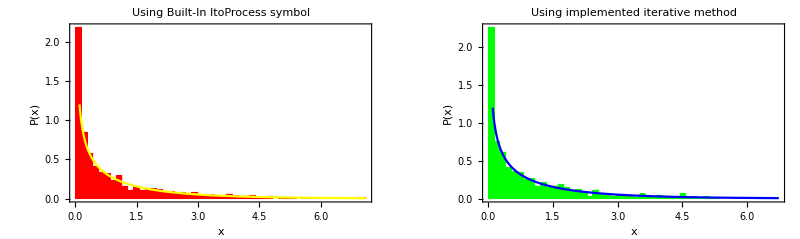

```mathematica
GraphicsRow[MapThread[
( 
max=RankedMax[#,n/100] ;Show[{Histogram[DeleteCases[#1,Overflow[]],{0,max,max/50},"PDF",ChartStyle->#2],Plot[P[x],{x,0.1,max},PlotStyle->#3]} 
,Frame->True
,PlotLabel->Style[#4,15]
,PlotRange->All
,FrameLabel->(Style[#,20]&/@{"x","P(x)"})
]
)&,
{{data$BuiltIn,data$iterative},{Red,Green},{Yellow,Blue},{"Using Built-In ItoProcess symbol","Using implemented iterative method"}}],ImageSize->Full]
```